# Kalman Folding versus Particle Filtering

Brian Beckman
16 Mar 2018

## Abstract

Kalman Folding is equivalent to Renormalized Recurrent Least Squares, and is Bayesian by construction (Beckman, 2018, https://goo.gl/CwLYjf). Therefore, it regularizes well. Sticking with concrete, numerical examples, we show that particle filtering can reproduce the results of Kalman Folding. For a more theoretical analysis, see Fernández-Villaverde (http://www.ssc.upenn.edu/~jesusfv/filters_format.pdf).

We show, by numerical examples, that Kalman folding (KAL) produces the same results as recurrent least squares (RLS) and maximum a-posteriori (MAP), for appropriate choices of a-priori covariances, i.e., regularization hyperparameters. KAL and RLS are more intuitive than MAP for practical applications, plus offer space-time efficiency over MAP by avoiding storage and multiplication of large matrices. Because RLS and KAL are overt recurrences, a-priori data are necessary to bootstrap them, so regularization is naturally built-in to the formulation: they are Bayesian by construction. Contrast MAP, wherein a-priori belief is introduced as a Bayesian modification of traditional, maximum-likelihood (MLE) least-squares through the normal equations. 

We exploit the novel fact that MAP is invariant when its hyperparameters are both swapped and inverted. After that transformation, the MAP equations strongly resemble the equations of Kalman filtering. This resemblance may suggest a future, general proof of the invariance, perhaps by conversion of MAP from explicit to recurrent form.

## Recurrence

Fold this recurrence over Ζ and A:

ξ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ξ)
Λ←(Λ+aᵀ·a)

where

ξ is the current estimate of Ξ

a and ζ are matched rows of A and Ζ

Λ accumulates Aᵀ·A.

### Derivation Sketch

Derive the recurrence as follows: Treat the estimate-so-far,

ξ_(so-far)=^def(Aᵀ·A)^-1·Aᵀ·Ζ_(so-far)

as just one more observation with information matrix

Λ=A_(so-far)ᵀ·A_(so-far)

The scalar performance or squared error of the estimate, so far, is

J(ξ)  =  (Ζ_(so-far)-A_(so-far)·ξ)ᵀ·(Ζ_(so-far)-A_(so-far)·ξ)  =  (ξ-ξ_(so-far))ᵀ·Λ·(ξ-ξ_(so-far))

where ξ is the unknown true parameter vector, Ζ_(so-far) is the column vector of all observations so-far, and Λ=A_(so-far)ᵀ·A_(so-far) . Adding a new observation, ζ and its corresponding partial row covector a, increases the error J(ξ) by (ζ-a·ξ)ᵀ·(ζ-a·ξ). Minimize the new total error with respect to ξ to find the recurrence (exercise). ■

We see that RLS perforce introduces an a-priori estimate ξ_0 and its covariance, which is the inverse of the information matrix Λ_0. RLS is Bayesian by construction. We show below that, when renormalized with an a-priori covariance for the observations ζ, is theoretically equivalent to KAL and numerically equivalent to MAP. Proof of theoretical equivalence to MAP awaits future work.

### Numerical Demonstration

Bootstrap the recurrence with ad-hoc, a-priori values ξ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ξ),Π}];

MatrixForm/@
({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

Transpose::nmtx: The first two levels of {data,partials} cannot be transposed.

{(-((0.+Transpose[partials].data) Transpose[partials].partials)/(1.×10^-12+2.×10^-6 Transpose[partials].partials)+((0.+Transpose[partials].data) (1.×10^-6+Transpose[partials].partials))/(1.×10^-12+2.×10^-6 Transpose[partials].partials)
-((0.+Transpose[partials].data) Transpose[partials].partials)/(1.×10^-12+2.×10^-6 Transpose[partials].partials)+((0.+Transpose[partials].data) (1.×10^-6+Transpose[partials].partials))/(1.×10^-12+2.×10^-6 Transpose[partials].partials)),(1.×10^-6+Transpose[partials].partials | Transpose[partials].partials
Transpose[partials].partials | 1.×10^-6+Transpose[partials].partials)}

The estimates mBar and bBar are, numerically, the same as we got from Wolfram’s built-in. For this example, the choice of ξ_0 and Λ_0 had negligible effect.

### Structural Notes

The mappings of List over the data and partials convert them into column vectors. Wolfram built-ins and the normal equations, implicitly, treat one-dimensional lists as columns or rows as needed, then compute inner (dot) products as if the distinction did not matter. Python’s numpy has the same dubious feature.

### Memory and Time Efficiency

The required memory for the recurrence is O(Μ), where Μ is the order of the model, the number of parameters to estimate, the length of Ξ, and the length of each row of A. There is no dependency at all on the number Ν of data items. Also, the recurrence accumulates data one observation at a time, and is thus O(Ν) in time. Contrast with the normal equations, which multiply at ~O(Ν^3) and invert at ~O(Μ), i.e., at much greater time cost.

### Check the A-Priori

The final value of Λ (called Π in the code, a returned value), is A_full ᵀ·A_full+Λ_0. To check the code, check that the difference between Π and A_full ᵀ·A_full is Λ_0:

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0},{0,1.×10^-6}}

### Covariance of the Estimate

The covariance of this estimate Ξ is ((n-1)/(n-2))*Variance [ Ζ-A·Ξ ]*Λ^-1 except for a small contribution from the a-priori information Λ_0. The correction factor ((n-1)/(n-2)) is a generalization .7fof Bessel’s correction. The 2 in (n-2) in the denominator of Bessel’s correction is the number of parameters being estimated (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

1/(-2+nData)(-1+nData) Inverse[Transpose[partials].partials] Variance[data-partials.{-((0.+Transpose[partials].data) Transpose[partials].partials)/(1.×10^-12+2.×10^-6 Transpose[partials].partials)+((0.+Transpose[partials].data) (1.×10^-6+Transpose[partials].partials))/(1.×10^-12+2.×10^-6 Transpose[partials].partials),-((0.+Transpose[partials].data) Transpose[partials].partials)/(1.×10^-12+2.×10^-6 Transpose[partials].partials)+((0.+Transpose[partials].data) (1.×10^-6+Transpose[partials].partials))/(1.×10^-12+2.×10^-6 Transpose[partials].partials)}]

Except for the reversed order, this is the same covariance matrix that Wolfram’s LinearModel reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[CovarianceMatrix].

model[Reverse[CovarianceMatrix]]

Don’t Invert That Matrix.7f

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/ 

In general, replace any occurrence of A^-1·B or Inverse[A].B with LinearSolve[A,B] for arbitrary square matrix A and arbitrary matrix B. Almost all programming languages and toolkits support an efficient and robust analogue to Wolfram’s LinearSolve.

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ξ)],Π}];

MatrixForm/@({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

Transpose::nmtx: The first two levels of {data,partials} cannot be transposed.

{((0.5 Transpose[partials].data)/(5.×10^-7+1. Transpose[partials].partials)
(0.5 Transpose[partials].data)/(5.×10^-7+1. Transpose[partials].partials)),(1.×10^-6+Transpose[partials].partials | Transpose[partials].partials
Transpose[partials].partials | 1.×10^-6+Transpose[partials].partials)}

Because this example is small, Inverse has no obvious numerical issues. It is very easy to produce large, ill-conditioned matrices, and one will spend a lot of time and storage inverting them, only to get useless results.

Interim Conclusions

We have eliminated memory bloat by processing updates one observation at a time, each with its paired partial. We reduce computation time and numerical risk by solving a linear systems instead of inverting a matrix. We also avoid multiplication of O(Ν) matrices, which is of approximately O(Ν^3) time.

## Regularization By A-Priori

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in their coefficients, starting in section 1.1. The higher the order of the polynomial, the more MLE over-fits. Bishop presents MAP regularization as a cure for this over-fitting. RLS and KAL already regularize, by construction. In this section, we relate their regularization to MAP’s.

RLS and KAL each require an a-priori estimate of the unknown parameters and an a-priori uncertainty of that estimate to bootstrap recurrences. RLS takes the uncertainty as an information matrix. KAL takes the uncertainty as a covariance matrix. KAL additionally requires an estimate of observation noise, which arises in real problems and can often be estimated out-of-band. We show that RLS can and should be renormalized with observation noise to produce results equivalent to KAL and MAP.

Reproducing Bishop’s Example

### Bishop’s Training Set

First, create a sequence of Ν=10 inputs for a training set, equally spaced in [0..1].

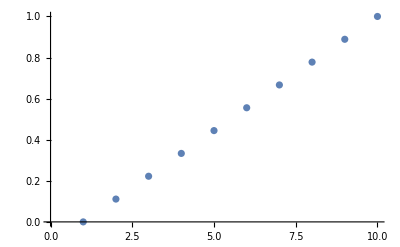

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[Ν_]:=Array[Identity,Ν,{0.,1.}];
ListPlot[bishopTrainingSetX[10]]
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the inputs of the training set above. Bishop doesn’t state an observation noise, but I guess σ_z=σ_t=0.30 to create a fake data set that resembles Bishop’s qualitatively.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample of the outputs and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

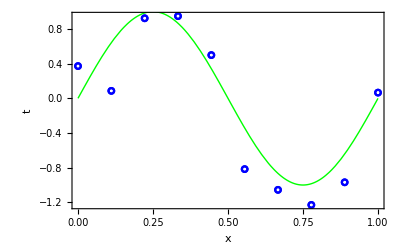

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

### Partials: Gradients of the Unknown Parameters

Write a function for partials. Quietly map the indeterminate 0^0 to 1. Test it symbolically.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
MatrixForm@partialsFn[6,{Subscript[x, 1],Subscript[x, 2],Subscript[x, Μ]}]
```

(1 | x_1 | x_1^2 | x_1^3 | x_1^4 | x_1^5 | x_1^6
1 | x_2 | x_2^2 | x_2^3 | x_2^4 | x_2^5 | x_2^6
1 | x_Μ | x_Μ^2 | x_Μ^3 | x_Μ^4 | x_Μ^5 | x_Μ^6)

### The MAP Equations

Confer Bishop’s equation 3.3, page 138, where he writes the parameters to estimate as w and the observation equation as

y(x, w)=∑_(j=0)^Μ w_j ϕ_j (x)

(bias incorporated as coefficient w_0 of 0^th basis function). This is predictive: you give me concrete inputs x, parameters w, and I’ll give you a predicted observation y in terms of Μ+1 basis functions ϕ corresponding to the Μ+1 unknown parameters. For polynomial basis functions, the number of parameters is one more than the order Μ of the polynomials. The basis functions can be anything, however: wavelets, Fourier components, etc.

Bishop (inexplicably) converts w into a covector and writes

y(x, w)=wᵀϕ (x)

where ϕ (x) is an (Μ+1)-dimensional column-vector of basis functions, the transpose of one row of our partials matrix A. We claim it’s better always to think of partials or gradients as values of differential forms, thus covectors (row vectors or covariant vectors, see https://goo.gl/DkeVmM, https://goo.gl/JgzqLR, and https://goo.gl/4TcF4T). 

To find best-fit values for w, rows of the partials matrix A are the covector gradients of y with respect to w. We prefer to write

observations as an Ν-dimensional column-vector Ζ_Ν with elements ζ_(j ∈ [ 1 ..Ν ])

the model or unknown parameters, an (Μ+1)-dimensional column-vector Ξ_((Μ+1)×1) with elements ξ_(i ∈ [ 0 ..Μ ])

partials matrix as A_(N×(Μ+1))

Bishop calls our partials matrix the design matrix in his equation 3.16, page 142, consisting of values of the basis functions at the concrete inputs x_(n ∈ [1..N]). Bishop must (more cumbersomely) work in the dual of our formulation. 

We prefer to write as follows: the covector rows of the design matrix terms as polynomial basis functions evaluated at the input points x_(n ∈ [1..Ν]):

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (1=x_1^0 | x_1 | x_1^2 | ⋯ | x_1^M
1=x_2^0 | x_2 | x_2^2 | ⋯ | x_2^M
⋮ | ⋮ |   | ⋱ | ⋮
1=x_N^0 | x_N | x_N^2 | ⋯ | x_N^M)  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

then packed up into rows of the A matrix.

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (A_(1×(Μ+1))(x_1)
A_(1×(Μ+1))(x_2)
⋮
A_(1×(Μ+1))(x_Ν))_(Ν×(Μ+1))  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

### MLE: The Normal Equations

Mechanize the normal equations for comparison purposes; we expect them to over-fit.

```mathematica
ClearAll[mleFit];
mleFit[Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
PseudoInverse[partialsFn[Μ,xs]].ys];
mleFit[3,bts]
```

{0.0182634,10.12,-32.1169,21.9763}

A convenience function:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

The normal equations as a symbolic polynomial. Notice we can increase the order beyond the number of data, creating an underdetermined system. This is not the typical case in real-world data processing. Usually the number of data exceed the order and the system is overdetermined. The pseudoinverse is agnostic to the distinction.

```mathematica
ClearAll[x];
Manipulate[
symbolicPowers[x,Μ].mleFit[Μ,bts],
{{Μ,3,"polynomial order Μ"},0,16,1,Appearance->{"Labeled"}}]
```

### RLS: Recurrent Least Squares

RLS is regularized by its a-priori estimate of the unknown parameters and its a-priori information matrix. Use the slider below to see that once the minimum info becomes too large, the Λ matrix becomes ill-conditioned: pink warning message appear from the Wolfram kernel, and the solution is numerically suspect. In the rest of this paper, we eliminate these error message by applying Wolfram’s Quiet because we notice, numerically, that ill-conditioning of the information matrix does not seem to be harmful.

```mathematica
ClearAll[rlsFit];
rlsFit[σ2Λ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2Λ*IdentityMatrix[Μ+1]},
Fold[update,{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ]]];

Manipulate[
rlsFit[10^-logσ2Λ][3,bts]⟦1⟧,
{{logσ2Λ,9.034},0,16,Appearance->"Labeled"}]
```

### KAL: Foldable Kalman Filter

The foldable Kalman filter (KAL) follows below. This version has only the update phase of a typical Kalman filter because the parameters-to-estimate are constant and there is no predict phase.

Note the P_Ζ parameter, the first in the definition of kalmanUpdate. This is the covariance matrix of the observation noise. It is a constant throughout the folding run of the filter. That’s why it’s lambda-lifted into its own function slot; kalmanUpdate, called with some concrete value of P_Ζ, yields a function that can be folded over an a-priori estimate ξ_0 and covariance P_0 and a sequence of observation-and-partial-covector pairs {ζ,a}.

```mathematica
ClearAll[kalmanUpdate,kalFit];
kalmanUpdate[PΖ_][{ξ_,P_},{ζ_,a_}]:=
Module[{D,KT,K,L},
D=PΖ+a.P.aᵀ;
KT=LinearSolve[D,a.P];K=KTᵀ;
L=IdentityMatrix[Length[P]]-K.a;
{ξ+K.(ζ-a.ξ),L.P}];

kalFit[σζ2_,σξ2_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,order+1],
P0=σξ2*IdentityMatrix[order+1]},
Fold[kalmanUpdate[σζ2*IdentityMatrix[1]],
{ξ0,P0},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
```

### See All Three

The following interactive demonstration shows mleFit (normal equations), rlsFit (recurrent least squares), and kalFit (Kalman folding) on Bishop’s training set.

When the a-priori information matrix in RLS is 10^-6, and when the a-priori covariance of the a-priori estimate in KAL is 10^6, both RLS and KAL produce regularized fits. In contrast, the MLE over-fits a 9^th-order polynomial by interpolating (going through) every data point because a 9^th-order polynomial fits the ten data points exactly: the normal equations are neither overdetermined nor underdetermined at order nine, but accidentally constitute an exactly solvable linear system.

Increasing -logΛ decreases the (magnitude of the) a-priori information matrix in RLS, meaning that we have less Bayesian belief in the a-priori estimate of the unknown parameters. Increasing logσξ2 increases the a-priori covariance of the estimate in KAL and similarly decreases belief in the a-priori estimate. They eventually both over-fit the data completely and align with MLE. Later, we show that MAP can be similarly made to over-fit. Run the polynomial order up to nine, then -logΛ and logσξ2 all the way to the right, to their maximum values.

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{
recurrent=Quiet@rlsFit[10^-logΛ0][Μ,bts],
normal=mleFit[Μ,bts],
kalman=kalFit[bishopFakeSigma^2,10^logσξ2][Μ,bts]},
With[{
rlsFn={terms}.recurrent⟦1⟧,
mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{
{Grid[{{
Button["RESET",(Μ=9;logΛ0=3;logσξ2=3)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,True,"MLE"},{True,False}}]}}]},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logΛ0,3,"-log a-priori info (RLS)"},0,16,Appearance->"Labeled"}]},{Control[{{logσξ2,3,"log a-priori cov (KAL)"},0,16,Appearance->"Labeled"}]}}]]
```

Renormalizing RLS

When the observation noise Ζ is unity, KAL coincides with RLS. In the demonstration below, a-priori information Λ in RLS is set always to be the inverse of a-priori estimate covariance P in KAL; RLS and KAL will have the same belief in the a-priori estimate of the unknown parameters. Vary the observation noise independently to see KAL and RLS coincide when it’s zero.

As observation noise decreases, the solutions believe the observations more and the solution over-fits. As the a-priori covariance decreases, the solution believes the a-priori estimates more and the solution regularizes.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{rls=Quiet@rlsFit[10^(-2logσξ)][Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{rlsFn={terms}.rls⟦1⟧,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(logσζ=0.0;logσξ=1.5;Μ=9)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}]}}],""},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}],""},{Control[{{logσξ,1.5,"log √P (KAL) = (-log √Λ) (RLS) "},-3,8,Appearance->"Labeled"}]},{Control[{{logσζ,0.0,"log √Ζ (KAL)"},-6,3,Appearance->"Labeled"}]}}]]
```

### Add Observation Noise to RLS

RLS, so far, is normalized to unit observation (OBN) noise. How to modify RLS to account for non-normalized OBN noise? 

Scale (each row of) the partials by the inverse of the OBN standard deviation, represented below by a matrix square root of the OBN covariance P_Ζ. Finally, rescale the final estimate (not the final covariance) by a matrix built from the inverse OBN standard deviation because the recurrent normal equations, which incrementally build (P_Ζ^-1·Aᵀ·A·P_Ζ^-T)^-1·P_Ζ^-1·Aᵀ·Ζ, have one too many factors of P_Ζ.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+Λ.ξ)],Π}]];

Manipulate[
With[{ξ0=({{0}, {0}}),Λ0=({{1.0*^-6, 0}, {0, 1.0*^-6}}),
inputs={List/@data⟦1;;n⟧,List/@partials⟦1;;n⟧}ᵀ},
Module[{ξrr,ξr,ξk,Πrr,Πr,Πk},
({ξrr,Πrr}=Fold[rlsUpdate[σ IdentityMatrix[1]],
{ξ0,Λ0},inputs]);
({ξr,Πr}=Fold[update,{ξ0,Λ0},inputs]);
({ξk,Πk}=Fold[kalmanUpdate[σ^2],{ξ0,Inverse@Λ0},inputs]);
MatrixForm@{
{(IdentityMatrix[2]/σ).ξrr,ξr,ξk},{Πrr,Πr/σ^2,Inverse@Πk},
{Chop[Abs[Πrr-Πr/σ^2],10^-6],
Chop[Abs[Inverse@Πk-Πr/σ^2],10^-6],
Chop[Abs[Inverse@Πk-Πrr],10^-6]}}]],
{{n,3},3,nData,1,Appearance->"Labeled"},
{{σ,1},-100,100,Appearance->"Labeled"}]
```

### RLS beats KAL

KAL and renormalized RLS are mathematically equivalent. Operationally, KAL uses subtraction to recur the covariance of the estimates, so is exposed to catastrophic cancelation. RLS only adds to the information matrix, so is exposed only to ill-conditioning, which is empirically less severe. We show this below.

## Regularization and MAP

Bishop reports β=11.111… and α=0.005 in his figure 1.17 (page 32) and in equations 1.70 through 1.72 (page 31), which look suspiciously like the equations for Kalman filtering. Bishop’s matrix S looks like D^-1 in kalmanUpdate above. Let’s reproduce MAP via RLS and KAL.

Bishop’s MAP

Bishop’s equations 1.70 through 1.72 are reproduced here. The dimensions of the identity matrix in S is Μ+1, where Μ is the order of the polynomial, one more than Μ to account for the leading bias term:

m(x)  =  β ϕ (x)ᵀ·S·∑_(n=1)^N ϕ (x_n)t_n

s^2(x)  =  β^-1+ϕ (x)ᵀ·S·ϕ (x)

S^-1  =^def  α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ

Here are links between Bishop’s formulation and ours, without derivation.

∑_(n=1)^N ϕ (x_n)t_n=Aᵀ·Ζ

lim_(α→0) ( β^-1 S^-1)=Aᵀ·A

### Φ Vectors

Bishop’s ϕ (x_n) is a (Μ+1)-dimensional column vector of the powers of the n^th input x_n. These powers are the basis functions of a polynomial model for the curve. ϕ (x_n) is the dual (transpose) of one row of our partials matrix A. 

As written, Bishop’s equations are non-recurrent, requiring all data t_n and ϕ (x_n) in memory. Plus, as written, they require inverting matrix S. They thus suffer from the operational ills of the normal equations.

```mathematica
ClearAll[ϕ];
ϕ[Μ_][xn_]:=Quiet@Table[xn^i,{i,0,Μ}]/.{Indeterminate->1};
MatrixForm/@ϕ[3]/@List/@bts⟦1⟧
```

{(1
0.
0.
0.),(1.
0.111111
0.0123457
0.00137174),(1.
0.222222
0.0493827
0.0109739),(1.
0.333333
0.111111
0.037037),(1.
0.444444
0.197531
0.0877915),(1.
0.555556
0.308642
0.171468),(1.
0.666667
0.444444
0.296296),(1.
0.777778
0.604938
0.470508),(1.
0.888889
0.790123
0.702332),(1.
1.
1.
1.)}

### S Inverse

Bishop’s equation 1.72.

```mathematica
ClearAll[sInv,α,β];
sInv[α_,β_,cs_,Μ_]:=
With[{Ν=Length[cs]},
α IdentityMatrix[Μ+1]+β Sum[cs⟦i⟧.cs⟦i⟧ᵀ,{i,Ν}]];
```

### MAP Mean

Bishop’s equation 1.70.

```mathematica
ClearAll[mapMean];
mapMean[α_,β_,x_,cs_,ts_,Μ_]:=
With[{Ν=Length@cs},
{β*ϕ[Μ][x]}.(* row of partials *)
LinearSolve[(* vector of coefficients *)
sInv[α,β,cs,Μ],
ts.cs]]⟦1,1⟧;
```

### A-Priori Variances α and β

Bishop defines β=1/σ_ζ^2, where σ_ζ is the standard deviation, from the model, of the prediction ζ. The prediction ζ is the value of the model on an arbitrary input ξ. Similarly, Bishop defines α=1/σ_ξ^2, where σ_ξ is the standard deviation of the a-priori distribution of the unknown parameter estimate ξ. 

We observe, numerically, that Bishop’s equations match RLS and KAL when β is σ_ξ^2 and when α=σ_ζ^2. We leave full proof to another paper, being satisfied with numerical evidence here. 

Semi-numerically, the proposition is true (above order 4, The following becomes taxing for Mathematica):

```mathematica
ClearAll[x,α,β,chopQ];
DynamicModule[{chopQ=False},
Manipulate[With[{cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧},
If[chopQ,Chop,Identity]@FullSimplify[mapMean[α,β,x,cs,ts,Μ]-mapMean[1/β,1/α,x,cs,ts,Μ]]],
Column[{Row[{Button["UN-CHOP",chopQ=False],"        ",
Button["CHOP",chopQ=True]}],
Control[{{Μ,2,"order Μ"},0,4,1,Appearance->{"Open","Labeled"}}]}]]]
```

The other two combinations, where β=1/σ_ζ^2 ⋀ α=σ_ζ^2 or β=σ_ξ^2 ⋀ α=1/σ_ξ^2 are not correct. Intuitively, these two combinations do not contain full information about the a-priori beliefs in both ζ and ξ, so we do not expect them to be correct. This fact can be demonstrated numerically.

In the following demonstration, the numerical evidence for equality of the two applications of MAP becomes overwhelming. MAP, RLS, and KAL match for all settings of σ_ξ^2, σ_ζ^2, Μ (order of the model), and assignments of α and β. The one deviation from perfect match concerns KAL. Explore the case where the order is around Μ=4. For high σ_ξ^2 (don’t believe the a-priori estimate of ξ) and low σ_ζz^2 (do believe the observational data), KAL fluctuates wildly. Why? The Kalman denominator D=P_ζ+aᵀ P_ξ a becomes nearly aᵀ P_ξ a. The Kalman gain, K=P_ξ aᵀ D^-1 is nearly a^-1. The covariance update, (I-K a)·P, becomes ill-conditioned, if not negative, because K a is near unity. 

Renormalized RLS does not suffer from these ills because it never subtracts. Renormalized RLS is still exposed to ill-conditioning of the information matrix, but that seems numerically to be less harmful to the final result. We wrap RLS in Quiet to suppress warnings. There is no free lunch; MAP also shows ill-conditioning and is similarly wrapped.

```mathematica
ClearAll[rrlsFit];
rrlsFit[σ2ζ_,σ2ξ_][Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,Μ+1],
Λ0=σ2ξ^-1*IdentityMatrix[Μ+1]},
Module[{ξ,Λ},
{ξ,Λ}=Fold[
rlsUpdate[√σ2ζ IdentityMatrix[1]],
{ξ0,Λ0},
{List/@ys,List/@partialsFn[Μ,xs]}ᵀ];
{ξ/√σ2ζ,Λ}]]];
```

```mathematica
DynamicModule[{αβBishop=True},
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧,σζ2=10.^(2logσζ),σξ2=10.^(2logσξ)},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[σζ2,σξ2][Μ,bts],
rrls=Quiet@rrlsFit[σζ2,σξ2][Μ,bts]},
With[{α=If[αβBishop,1/σξ2,σζ2],β=If[αβBishop,1/σζ2,σξ2]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
mapFn=Quiet@mapMean[α,β,x,cs,ts,Μ],
rlsFn={terms}.rrls⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
If[mapQ,AppendTo[showlist,Plot[mapFn,{x,0,1},PlotStyle->{Magenta}]]];
Quiet@Show[showlist,Frame->True,ImageSize->Medium,FrameLabel->{{"ζ",""},{"ξ",Grid[{{"α: ",α,"β:",β}}]
}}]]]]]]]],
Column[{SetterBar[Dynamic[αβBishop],{True->"α = 1/σ_ξ^2, β = 1/σ_ζ^2",False->"α = σ_ζ^2, β = σ_ξ^2"}],
Row[{Button["RESET",(Μ=4;logσξ=.5;logσζ=-1.5)&],
Control[{{kalQ,True,"        KAL"},{True,False}}],
Control[{{rlsQ,True,"        RLS"},{True,False}}],
Control[{{mleQ,False,"        MLE"},{True,False}}],
Control[{{mapQ,True,"        MAP"},{True,False}}]},Frame->All],
Control[{{Μ,4,"order Μ"},0,16,1,Appearance->{"Labeled"}}],Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}],
Control[{{logσζ,-1.5,"log σζ (KAL)"},-7,3,Appearance->"Labeled"}]}]]]
```

### Covariance of the Estimate

Consider Bishop' s equation 1.71 s^2(x)=β^-1+ϕ (x)ᵀ·S·ϕ (x), which does not depend on the output data t_n, just as with KAL and RLS.7f.

```mathematica
ClearAll[mapsSquared];
mapsSquared[α_,β_,x_,cs_,Μ_]:=
With[{a=ϕ[Μ][x]},
β^-1+{a}.LinearSolve[sInv[α,β,cs,Μ],List/@a]];
```

Bishop kindly supplies the sigma-bars for his mean. He cites α=0.005 and β=11.1, which correspond to σ_ζ=0.07071 and σ_ξ=3.333, and log_10 σ_ζ=-1.15051 and log_10 σ_ξ=0.5229. These values reproduce Bishop’s figure 1.17 well.

Kalman’s output covariance P and RLS’s output information Π represent uncertainty in the estimated coefficients. These do not directly yield uncertainties in the predicted labels, i.e., polynomials evaluated at each input point. For those, we follow Bishop’s analysis and his equation 1.71.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
bs2=mapsSquared[10^(2logσζ),10^(2logσξ),x,cs,Μ],
mapFn=Quiet@mapMean[10^(2logσζ),10^(2logσξ),x,cs,ts,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,
Plot[{kalFn,kalFn+√bs2,kalFn-√bs2},{x,0,1},
PlotStyle->{Cyan,{Thin,{Opacity[0],Cyan}},{Thin,{Opacity[0],Cyan}}},Filling->{1->{2},1->{3}}]]];
If[mapQ,AppendTo[showlist,
Plot[{mapFn,mapFn+√bs2,mapFn-√bs2},
{x,0,1},
PlotStyle->{Magenta,{Thin,{Opacity[0],Magenta}},{Thin,{Opacity[0],Magenta}}},
Filling->{1->{2},1->{3}}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(Μ=9;logσξ=Log10[√(1/0.09)];logσζ=Log10[√0.005])&],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,False,"MLE"},{True,False}}],
Control[{{mapQ,True,"MAP"},{True,False}}]}}]},{Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logσξ,Log10[√(1/0.09)],"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}]},
{Control[{{logσζ,Log10[√0.005],"log σζ (KAL)"},-5,3,Appearance->"Labeled"}]}}]]
```

## Appendix: Particle Filter

Each particle ξ^i,i∈[1.. N_s], is an (Μ+1)-vector guess at the state, i.e., the column vector of coefficients. There are N_s of them for each time tick in the simulation.

```mathematica
ClearAll[σ0,P,P0,ξ0,ξ0s,importanceFunction];
ClearAll[Ns,σ0,σ,ξ,importanceFunctions,ξs,Μ,ws];

Ns=1000;

Μ=9;

σ0=10.^6;
σ[0]=List/@ConstantArray[σ0,Μ+1];

ξ[0]=List/@ConstantArray[0.,Μ+1];

importanceFunctions[t_]:=
Table[
NormalDistribution[ξ[t]⟦i,1⟧,σ[t]⟦i,1⟧],
{i,Μ+1}];

ξs[0]=
Table[
ξ[0]⟦i,1⟧+RandomVariate[importanceFunctions[0]⟦i⟧],
{i,Μ+1},{j,Ns}];

Print[<|"σ"->σ,"Dimensions[ξs[0]]"->Dimensions[ξs[0]]|>];

ws[0]=ConstantArray[1./Ns,Ns];
Plus@@ws[0]
```

<|σ→σ,Dimensions[ξs[0]]→{10,1000}|>

1.

### Check Covariance

```mathematica
With[{μ=Mean/@ξs[0]},μ]
```

{-14021.9,17014.2,-18064.2,-6978.02,2656.87,30785.7,27080.2,-16418.1,22805.7,-19119.8}

```mathematica
With[{μ=Mean/@ξs[0]},
With[{r=ξs[0]⟦All,All⟧-μ},
Sqrt[Diagonal[r.rᵀ]/(Ns-1)]]]
```

{1.03112×10^6,962365.,1.00197×10^6,997723.,1.00624×10^6,961100.,1.00483×10^6,973222.,1.00322×10^6,1.02298×10^6}

```mathematica
StandardDeviation/@ξs[0]
```

{1.03112×10^6,962365.,1.00197×10^6,997723.,1.00624×10^6,961100.,1.00483×10^6,973222.,1.00322×10^6,1.02298×10^6}

### 2D Point Clouds

```mathematica
DynamicModule[{i=1,j=2},
Manipulate[
ListPlot[{ξs[0]⟦i,All⟧,ξs[0]⟦j,All⟧}ᵀ,
PlotRange->3{{-σ0,σ0},{-σ0,σ0}},
AspectRatio->1,
Frame->True,FrameLabel->{
{"Dimension "<>ToString[j],""},
{"Dimension "<>ToString[i],
"Particle cloud, two dimensions at a time"}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]}}]]]
```

### 3D Point Clouds

```mathematica
ClearAll[threeDPointClouds];
threeDPointClouds[ξs_,σ_]:=
DynamicModule[{i=1,j=2,k=3},
Manipulate[Graphics3D[Point/@({ξs⟦i,All⟧,ξs⟦j,All⟧,ξs⟦k,All⟧}ᵀ),
Axes->True,AspectRatio->1,
AxesLabel->{"i: "<>ToString[i],"j: "<>ToString[j],"k: "<>ToString[k]},PlotRange->3{{-σ,σ},{-σ,σ},{-σ,σ}}],
Grid[{
{"i",SetterBar[Dynamic[i],Range[Μ+1]]},
{"j",SetterBar[Dynamic[j],Range[Μ+1]]},
{"k",SetterBar[Dynamic[k],Range[Μ+1]]}}]]];
threeDPointClouds[ξs[0],σ0]
```

### Inspect the Initial Particles

Get a columns of ξs[0]:

```mathematica
ClearAll[ξcol];
ξcol[t_,n_/;(1≤n≤Ns)]:=List/@ξs[t]⟦All,n⟧;
ξcol[0,41]//MatrixForm
```

(1.25013×10^6
-627607.
-513136.
703040.
1.06425×10^6
588728.
2.07372×10^6
-615101.
608979.
-618246.)

```mathematica
Manipulate[
partialsFn[m,bts⟦1⟧]//MatrixForm,
{{m,1},0,Μ+1,1,Appearance->{"Open","Labeled"}}]
```

```mathematica
partialsFn[Μ,bts⟦1⟧].ξcol[0,1]
```

{{-119629.},{-25863.1},{69443.3},{175702.},{299958.},{441985.},{585736.},{684654.},{637613.},{251571.}}

### Observations and Residuals

Observations are constant with time, but we include a time parameter just for fun. The particle cloud changes with time.

```mathematica
ClearAll[ζcol];
ζcol[t_]:=List/@bts⟦2⟧
```

```mathematica
ClearAll[residuals];
residuals[t_,n_/;1≤n≤Ns]:=
partialsFn[Μ,bts⟦1⟧].ξcol[t,n]-ζcol[t];
```

### Sum of Squared Residuals (SSR)

```mathematica
ClearAll[ssr];
ssr[t_,n_/;1≤n≤Ns]:=(residuals[t,n]ᵀ.residuals[t,n])⟦1,1⟧;
```

```mathematica
ClearAll[ssrs];
(ssrs=ssr[0,#]&/@Range[Ns])//Short
```

{1.61768×10^12,1.94241×10^13,«997»,7.8915×10^13}

### New Weights

Larger SSR means further from the observations. Let weights be inversely proportional to SSR, with divide-by-zero intentionally faulting because a zero SSR would signal an extremely improbable situation, most likely a bug somewhere else in the software.

```mathematica
(ws[1]= 1/ssrs/Plus@@(1/ssrs))//Short
```

{0.00309311,0.000257601,«997»,0.0000634058}

Check:

```mathematica
Plus@@ws[1]
```

1.

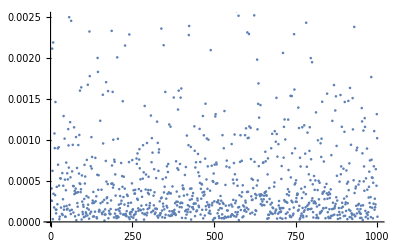

```mathematica
ListPlot[ws[1]]
```

### Cull the Particles

Keep only the particles that “do well” for the next time step, by some criterion driven by hyperparameters.

Pair each particle with its index:

```mathematica
ClearAll[indexedWeights];
(indexedWeights=MapThread[List,{Range[Ns],ws[1]}])//Short
```

{{1,0.00309311},«998»,{1000,0.0000634058}}

Keep the top (p=25)%. In general, p should be the reciprocal of an integer that divides N_s because we are going to copy each survivor 1/p times to make a new sample of size N_s.

```mathematica
ClearAll[p,sortedIndexedWeights,topPWeights,topPIndexedWeights,topPIndices,topPParticles];
p=0.25;
<|"sortedIndexedWeights"->((sortedIndexedWeights=Reverse@SortBy[indexedWeights,Last])//Short),
"topPIndexedWeights"->((topPIndexedWeights=sortedIndexedWeights⟦;;Floor[p Ns]⟧)//Short),
"topPWeights"->((topPWeights=Last/@topPIndexedWeights)//Short),
"topPIndices"->((topPIndices=First/@topPIndexedWeights)//Short),
"topPParticles//Dims"->((topPParticles=(ξs[0]⟦All,#⟧&/@topPIndices)ᵀ)//Dimensions),
"top 3 Particles"->(topPParticles⟦All,1;;3⟧//MatrixForm)|>
```

<|sortedIndexedWeights→{{842,0.0433785},«998»,{165,0.0000161703}},topPIndexedWeights→{{842,0.0433785},«248»,{977,0.000749295}},topPWeights→{0.0433785,0.0333407,«247»,0.000749295},topPIndices→{842,151,369,10,880,311,409,866,548,683,«230»,263,473,613,797,271,195,982,111,250,977},topPParticles//Dims→{10,250},top 3 Particles→(134190. | 47502.1 | 219276.
-365231. | -134588. | -1.28181×10^6
303295. | -313693. | 1.23859×10^6
-678022. | 1.19583×10^6 | 156514.
2.77311×10^6 | 36189.7 | 728030.
-1.07193×10^6 | -1.3026×10^6 | -159213.
-895601. | -138746. | -629400.
-420479. | 1.09658×10^6 | -228260.
-23471.3 | -251128. | 381432.
128797. | -607524. | -223408.)|>

Structure emerges after culling.

```mathematica
threeDPointClouds[topPParticles,σ0]
```

### Means of Top p Particles

```mathematica
ClearAll[μσ,μξ];
μξ[1]=Mean/@topPParticles
```

{15024.9,-23391.3,23971.2,-92318.9,13724.,-65019.5,59742.7,8210.52,41970.6,41953.9}

### Standard Deviations of Top p Particles

```mathematica
ClearAll[σξ];
σξ[1]=StandardDeviation/@topPParticles
```

{490553.,749260.,911202.,931565.,964104.,929876.,925945.,972763.,956935.,954751.}

Replace each particle with four (1/p) copies, each perturbed by this new σ_1. There are other ways to compute an importance sample of the top p particles. One way, possibly biased, is to keep the original survivor and add three perturbed copies. We first perform this latter sample (original joined to three copies) to check matrix dimensions, but proceed with the former sample (four copies).

#### Check Matrix Dimensions

Exhibit an example:

```mathematica
topPParticles⟦All,41⟧//MatrixForm
```

(-269514.
520496.
1.30612×10^6
-1.75133×10^6
-302433.
105183.
-630146.
308931.
672240.
964306.)

```mathematica
ClearAll[conjColumns];
conjColumns[m1_,m2_]:=((m1ᵀ)~Join~(m2ᵀ))ᵀ;
```

Check that the original appears in the first column.

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]-1},
conjColumns[
List/@ξ,
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(-269514. | -336345. | -881084. | 107212.
520496. | -394890. | 969037. | 668569.
1.30612×10^6 | 686645. | 470693. | 793276.
-1.75133×10^6 | 226693. | -718329. | -1.92153×10^6
-302433. | 1.17236×10^6 | -331396. | 634568.
105183. | 471103. | 425119. | -647397.
-630146. | -1.81463×10^6 | 363711. | -1.75716×10^6
308931. | -294025. | -901260. | 829348.
672240. | 495974. | 1.64415×10^6 | 1.19423×10^6
964306. | -35884.5 | 25588.5 | -78417.4)

#### Unbiased? Importance Sample

```mathematica
ClearAll[make1OverP];
make1OverP[ξ_,σξ_,p_]:=
With[{n=Floor[1/p]},
Table[
RandomVariate[NormalDistribution[ξ⟦m⟧,σξ⟦m⟧],n],
{m,Μ+1}]];
make1OverP[topPParticles⟦All,41⟧,σξ[1],p]//MatrixForm
```

(-41914.9 | -981092. | -483579. | 71741.9
1.69661×10^6 | 25355.5 | 1.13729×10^6 | 1.57507×10^6
344560. | -358666. | 2.6263×10^6 | 1.12021×10^6
-223828. | -1.56702×10^6 | -1.47672×10^6 | -2.22046×10^6
-584784. | -893832. | -3.11151×10^6 | -1.25877×10^6
-90366.8 | -397814. | 452374. | -222681.
-1.95568×10^6 | -2.13214×10^6 | -567739. | -2.1971×10^6
-87977.8 | 1.23401×10^6 | -411787. | -315499.
-1.6507×10^6 | 1.57436×10^6 | -45547.8 | -256743.
3.38819×10^6 | 687666. | 2.90737×10^6 | 2.72356×10^6)

### A New Particle Cloud

```mathematica
topPParticles//Dimensions
```

{10,250}

```mathematica
(ξs[1]=Fold[conjColumns,make1OverP[#,σξ[1],p]&/@(topPParticlesᵀ)])//Dimensions
```

{10,1000}

```mathematica
threeDPointClouds[ξs[1],σ0]
```

### Package and Iterate

Abstract the procedure witnessed above and iterate.

## Conclusion

We have shown that Kalman folding (KAL) produces the same results as renormalized recurrent least squares (RLS) and maximum a-posteriori (MAP) for appropriate choices of covariances, i.e., regularization hyperparameters. We have further shown (numerically) that MAP produces the same results when its hyperparameters are swapped and inverted. 

KAL and RLS offer significant advantages in space-time efficiency by avoiding storage and multiplication of large matrices. In all cases, we avoid matrix inverses by solving linear systems internally.